```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]
InstallFeynCalc[]
```

Downloading FeynCalc from https://github.com/FeynCalc/feyncalc/archive/hotfix-stable.zip ...done! 
FeynCalc zip file was saved to /var/folders/_b/4h7cqkb96yx26rk7lnjkzgcc0000gn/T/m000006690771.
Extracting FeynCalc zip file to /var/folders/_b/4h7cqkb96yx26rk7lnjkzgcc0000gn/T/m000006690771.dir ...done! 
Copying FeynCalc to /Users/tobiastheil/Library/Mathematica/Applications/FeynCalc ...done! 
Setting up the help system... done! 
Downloading FeynArts from https://github.com/FeynCalc/feynarts-mirror/archive/master.zip ...done! 
FeynArts zip file was saved to /var/folders/_b/4h7cqkb96yx26rk7lnjkzgcc0000gn/T/m000009690771.
Extracting FeynArts zip file to /Users/tobiastheil/Library/Mathematica/Applications/FeynCalc/FeynArts ...done! 
Copying FeynArts to /Users/tobiastheil/Library/Mathematica/Applications/FeynCalc/FeynArts ...done! 

Installation complete! Loading FeynCalc... 
Patching FeynArts... done!

FeynCalc::tfadvice: You are not using TraditionalForm as the default format type of new output cells. Without TraditionalForm FeynCalc cannot use built-in typeseting rules that make various objects like Lorentz vectors or Dirac matrices look nicer. To change the format type go to Edit->Preferences->Evaluation.

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

```mathematica
<<FeynArts`
```

Get::noopen: Cannot open FeynArts`.

$Failed

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

TopologyList[Process→{F[2,{1}]}→{F[2,{Gen2}],S[1]},Model→{SM},GenericModel→{Lorentz},InsertionLevel→{Generic,Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][4],Field[1]],Propagator[Outgoing][Vertex[1][2],Vertex[3][4],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][4],Field[3]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→F[2,{1}],Field[2]→-F[2,{Gen2}],Field[3]→S[1]]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{Gen2}],Field[3]→S[1]]]]]

> Top. 1: 2 diagrams

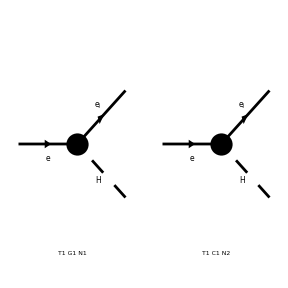

FeynArtsGraphics[{e}→{ComposedChar[e,j],H}][([T1 G1 N1] | [T1 C1 N2] | Null | Null
Null | Null | Null | Null
Null | Null | Null | Null
Null | Null | Null | Null)]

```mathematica
t12=CreateTopologies[0,1->2];
InsertFields[t12,F[2,{1}]-> {F[2],S[1]}]
Paint[%,ColumnsXRows->4]
```